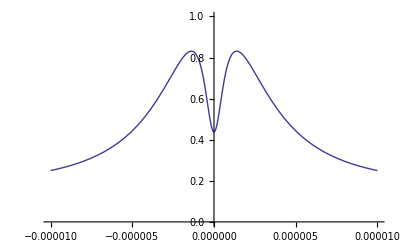

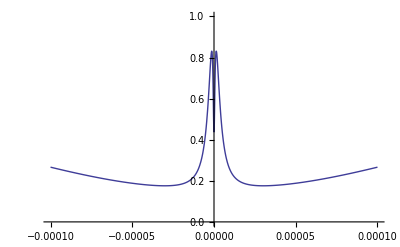

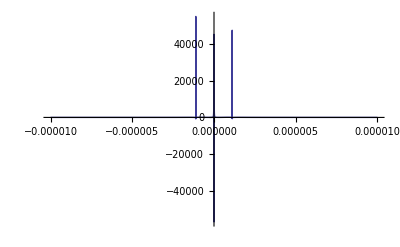

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=1× 10^7
Q2:=5× 10^9
Q3:= 6 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=0.41
x2:=0.0012
x3:=0.00000218
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00001;
δ1max:=0.00001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
(*Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]*)
```

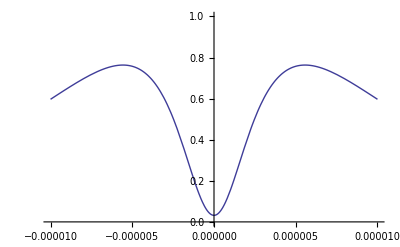

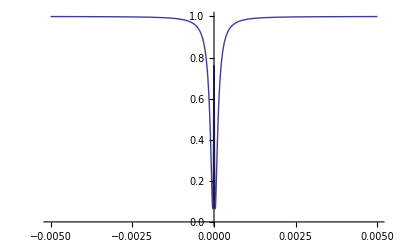

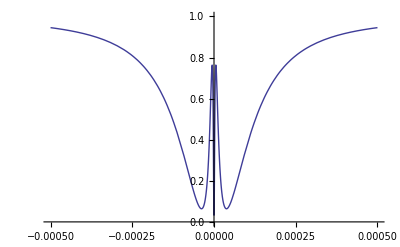

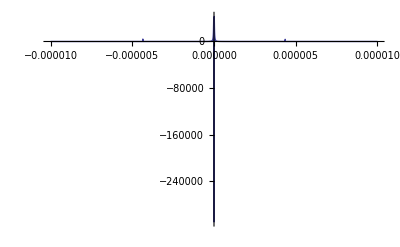

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=4× 10^7
Q2:=3× 10^9
Q3:= 2 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=1.7
x2:=0.0012
x3:=0.0000108
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00001;
δ1max:=0.00001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
(*Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]*)
```

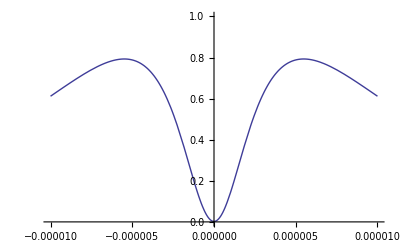

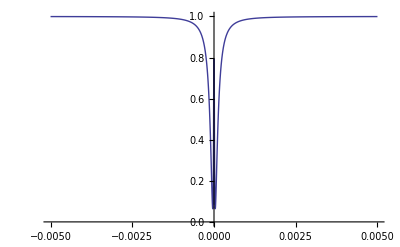

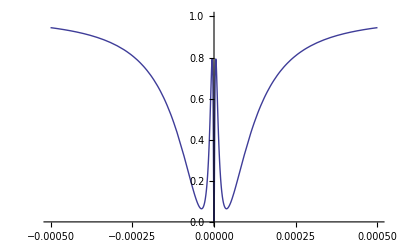

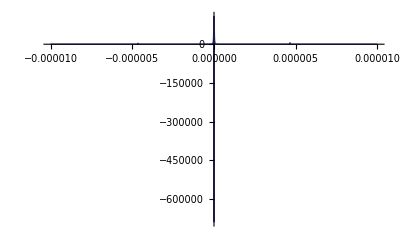

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=4× 10^7
Q2:=3× 10^9
Q3:= 3× 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=1.7
x2:=0.0012
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00001;
δ1max:=0.00001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
(*Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]*)
```

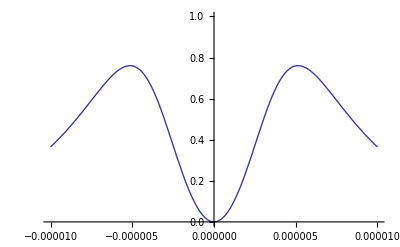

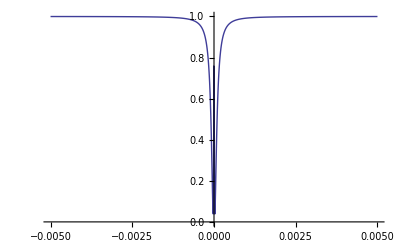

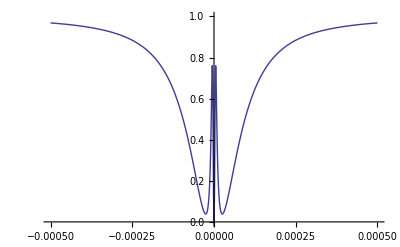

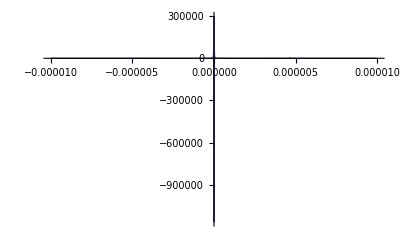

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=5× 10^7
Q2:=7× 10^9
Q3:= 3 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=1.5
x2:=0.0012
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00001;
δ1max:=0.00001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
(*Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]*)
```

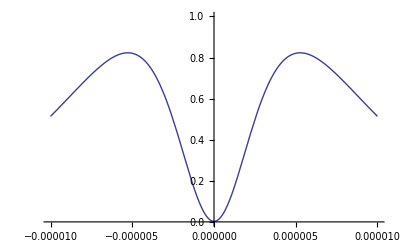

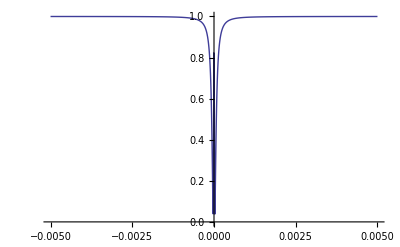

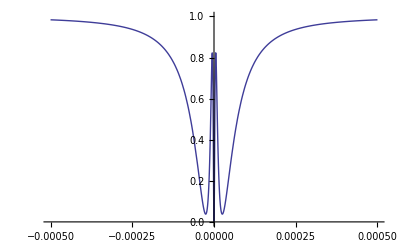

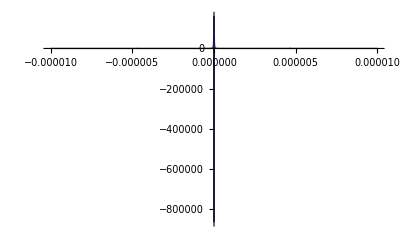

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=7× 10^7
Q2:=7× 10^9
Q3:= 3 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=1.5
x2:=0.0012
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00001;
δ1max:=0.00001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
(*Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]*)
```

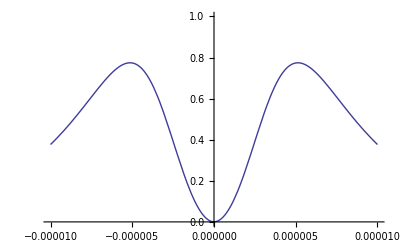

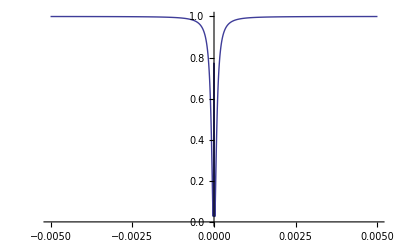

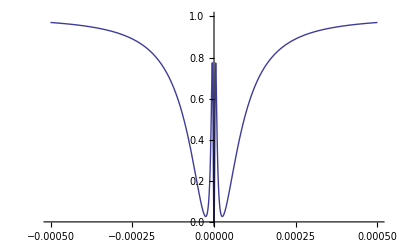

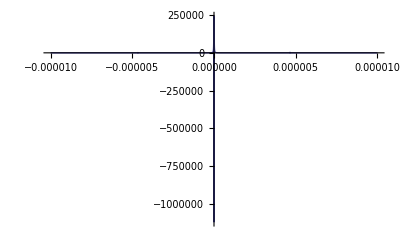

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=5× 10^7
Q2:=7× 10^9
Q3:= 3 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=1.4
x2:=0.0012
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00001;
δ1max:=0.00001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
(*Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]*)
```

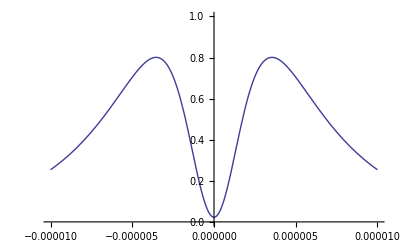

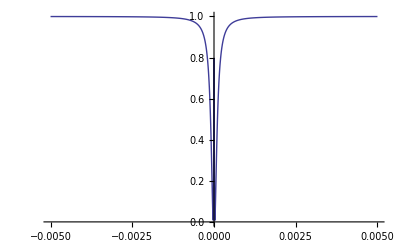

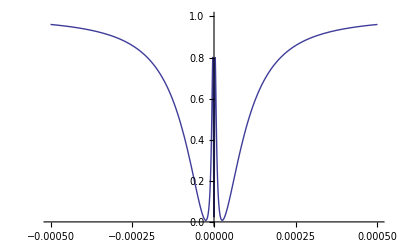

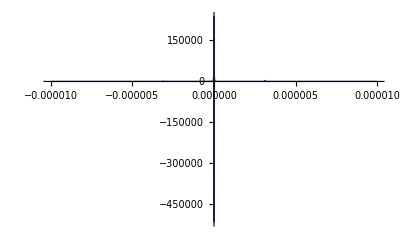

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=4× 10^7
Q2:=7× 10^9
Q3:= 4 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=1.2
x2:=0.0012
x3:=0.0000108
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00001;
δ1max:=0.00001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
(*Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]*)
```

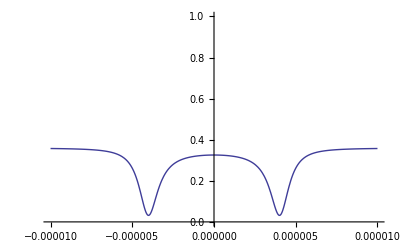

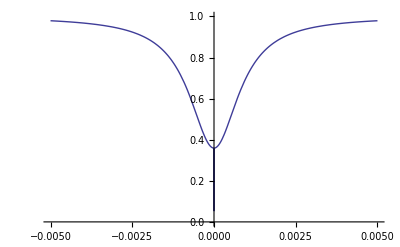

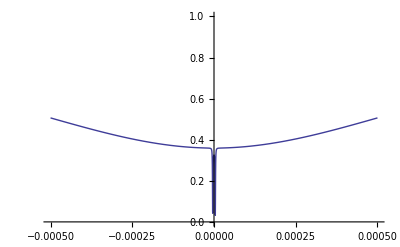

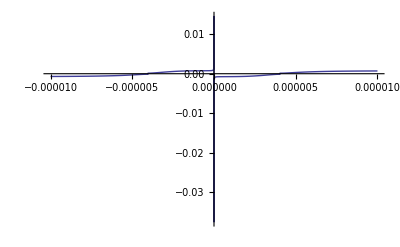

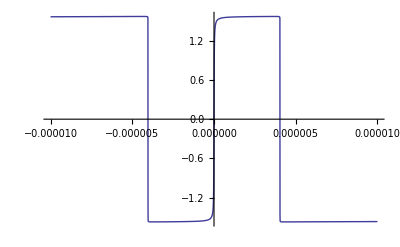

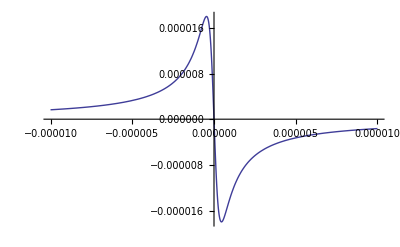

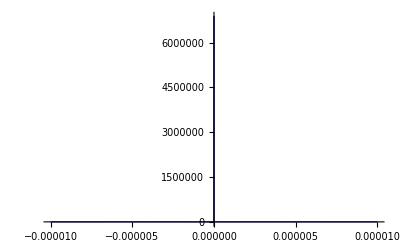

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=1× 10^7
Q2:=7× 10^9
Q3:= 4 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=4
x2:=0.0012
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00001;
δ1max:=0.00001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

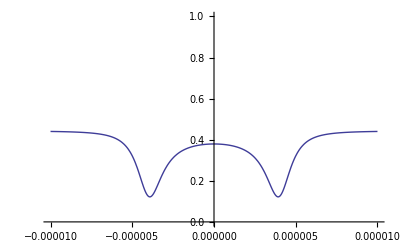

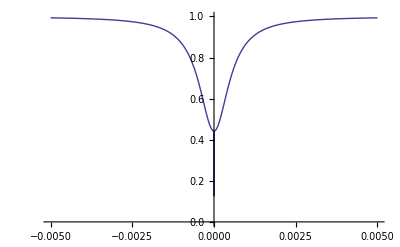

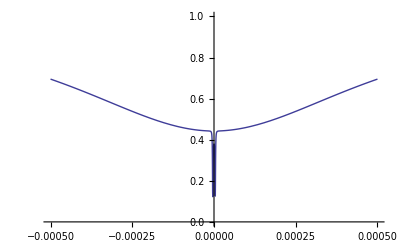

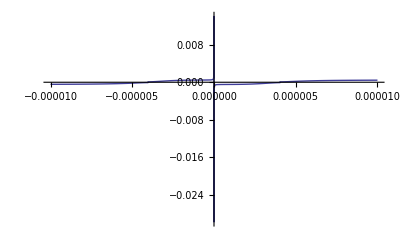

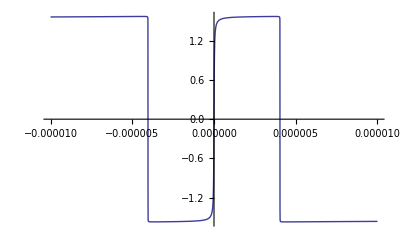

-Graphics-

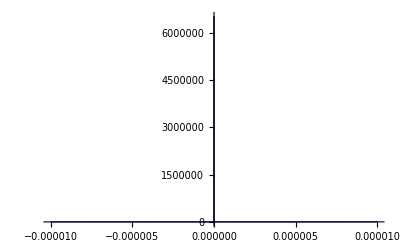

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=2× 10^7
Q2:=7× 10^9
Q3:= 4 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=5
x2:=0.0012
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00001;
δ1max:=0.00001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=4× 10^7
Q2:=7× 10^9
Q3:= 4 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=4
x2:=0.0012
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00001;
δ1max:=0.00001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[ref^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

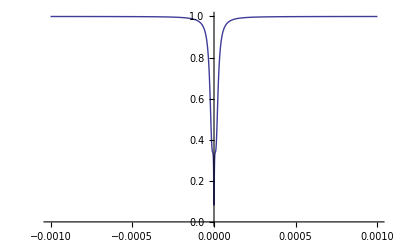

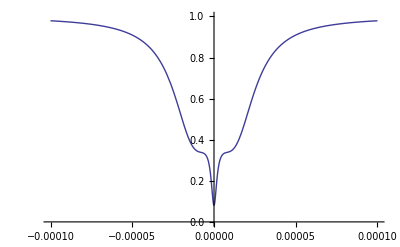

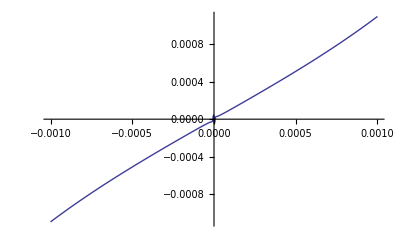

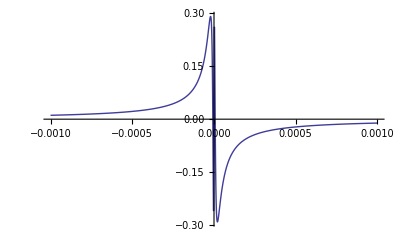

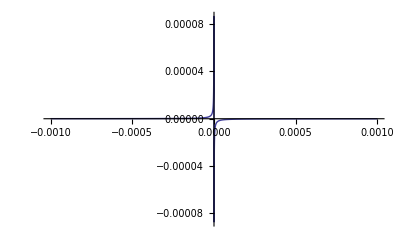

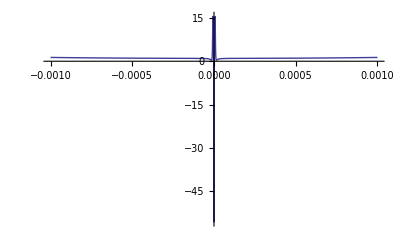

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=2× 10^8
Q2:=1× 10^8
Q3:= 7× 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=0.6
x2:=0.0000042
x3:=0.0001
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.001;
δ1max:=0.001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

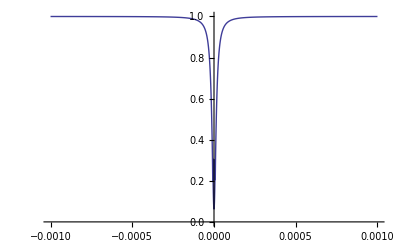

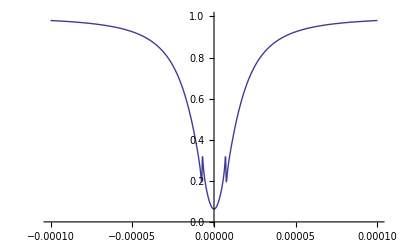

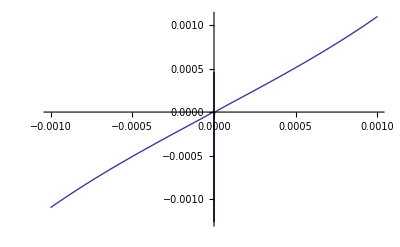

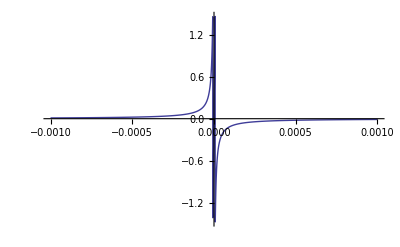

-Graphics-

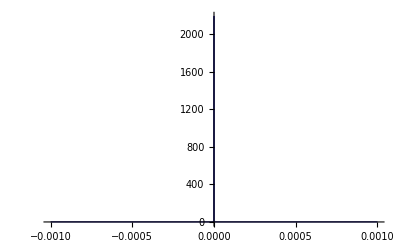

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=2× 10^8
Q2:=7× 10^9
Q3:= 7× 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=0.6
x2:=0.0000042
x3:=0.0001
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.001;
δ1max:=0.001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

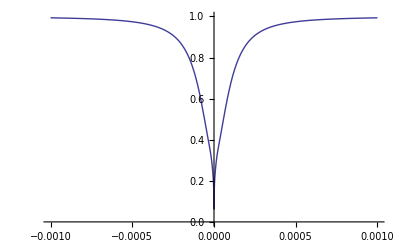

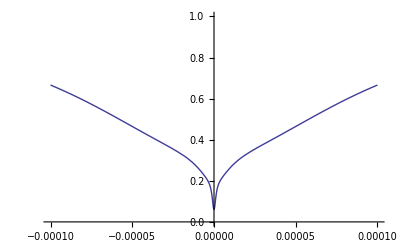

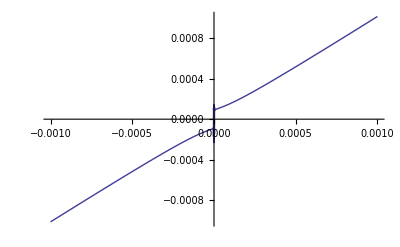

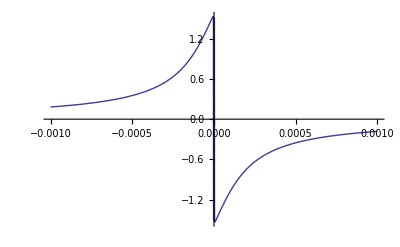

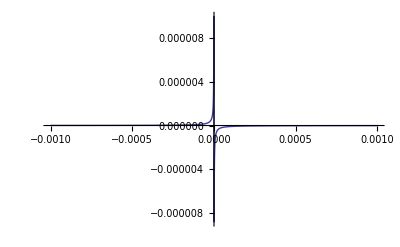

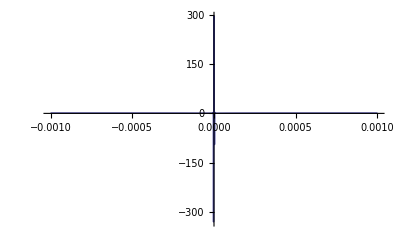

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=1× 10^8
Q2:=5× 10^8
Q3:= 4 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=5
x2:=0.00012
x3:=0.00001
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.001;
δ1max:=0.001;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

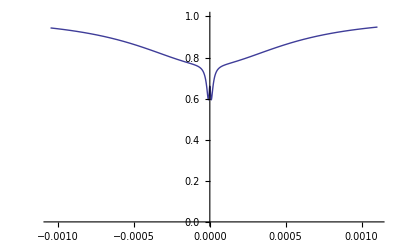

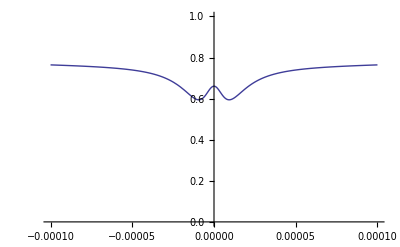

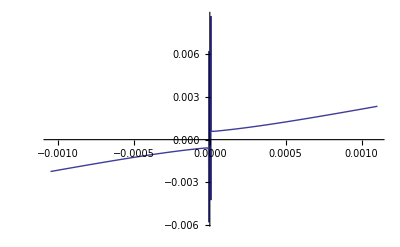

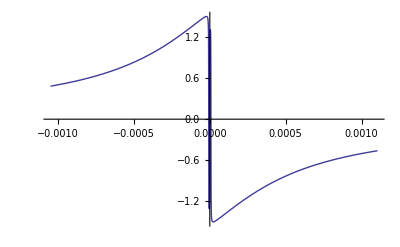

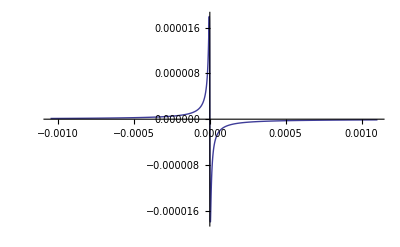

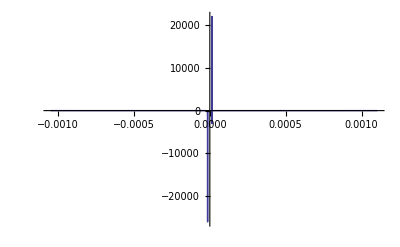

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 200 10^(-6)
R3:= 200 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=5× 10^7
Q2:= 1 × 10^8
Q3:= 5 × 10^8
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=15
x2:=0.00002
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00105;
δ1max:=0.001105;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

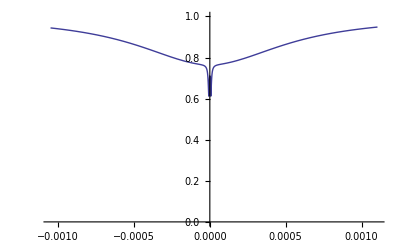

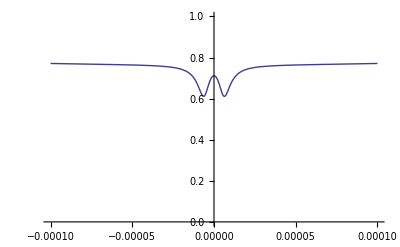

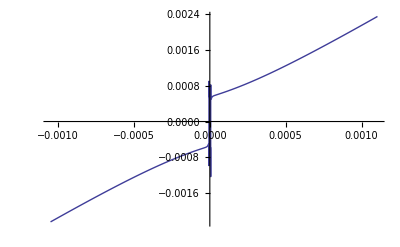

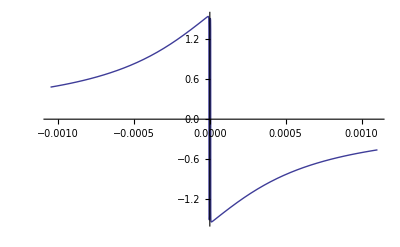

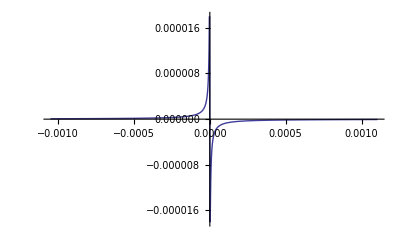

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 200 10^(-6)
R3:= 200 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=5× 10^7
Q2:= 3 × 10^8
Q3:= 9 × 10^8
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=15
x2:=0.00002
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00105;
δ1max:=0.001105;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

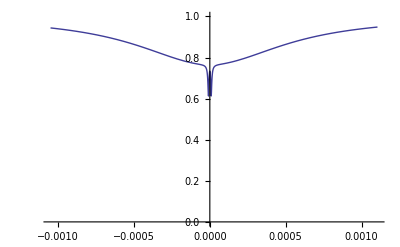

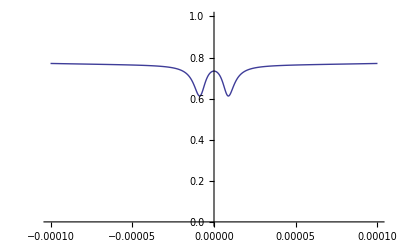

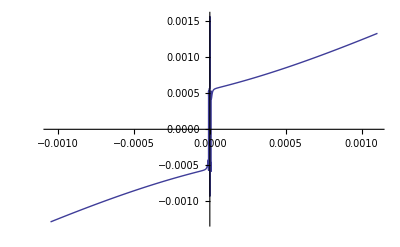

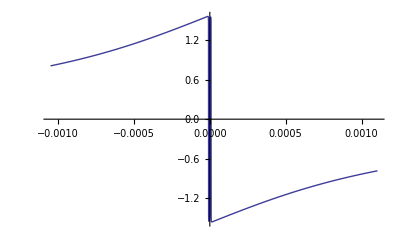

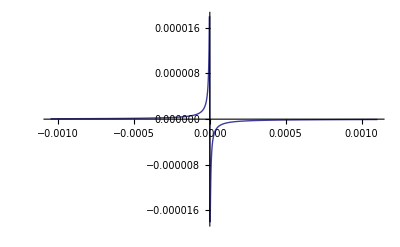

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=5× 10^7
Q2:= 3 × 10^8
Q3:= 9 × 10^8
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=15
x2:=0.00002
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00105;
δ1max:=0.001105;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[groupindex,{δ1,δ1min,δ1max}, PlotRange->All]
```

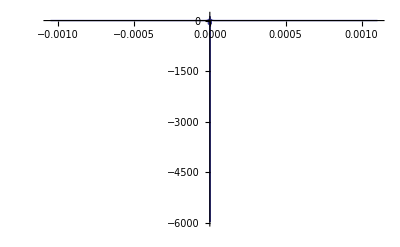

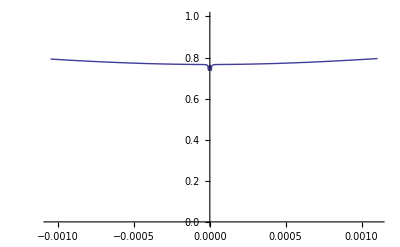

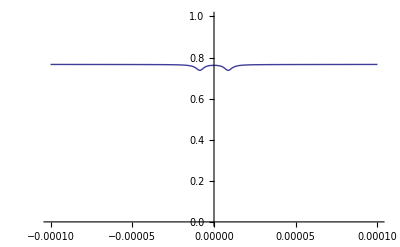

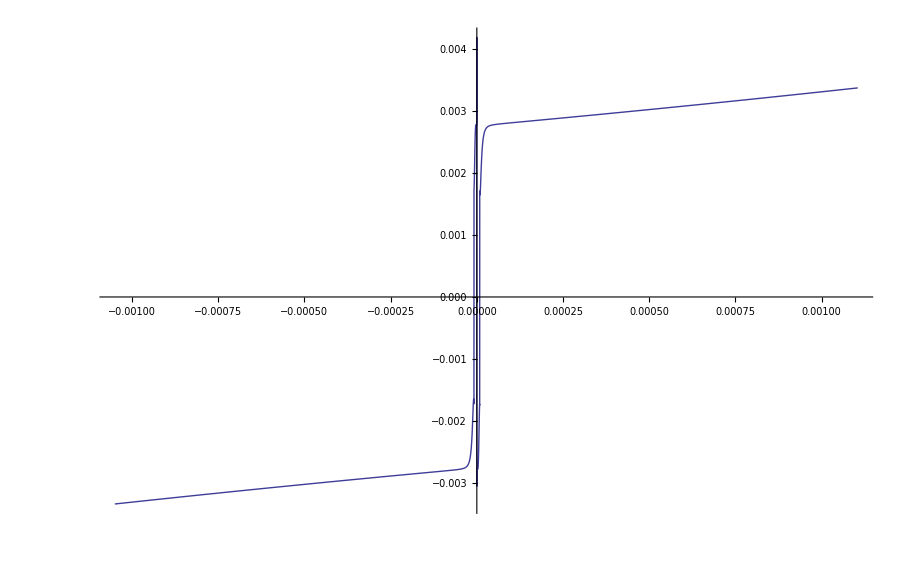

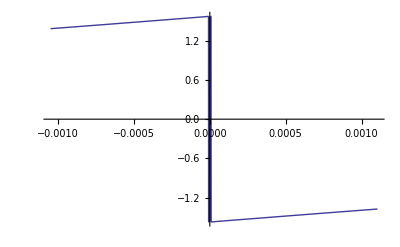

-Graphics-

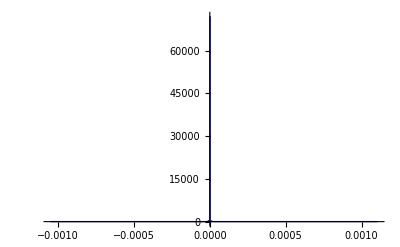

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=1× 10^7
Q2:= 5 × 10^8
Q3:= 9 × 10^8
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=15
x2:=0.00002
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00105;
δ1max:=0.001105;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

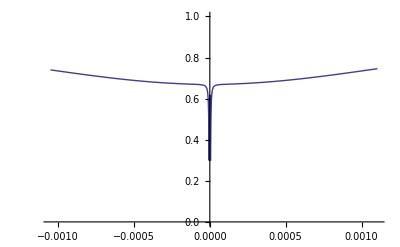

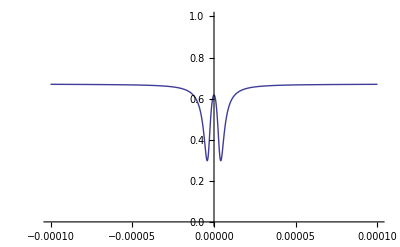

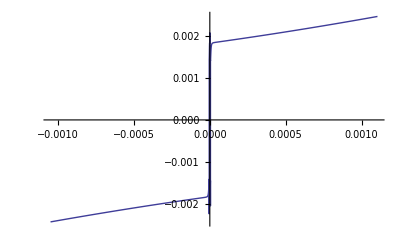

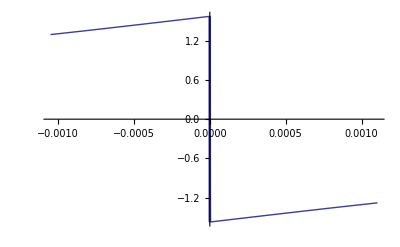

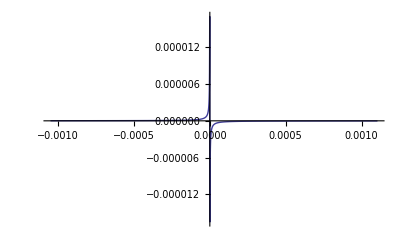

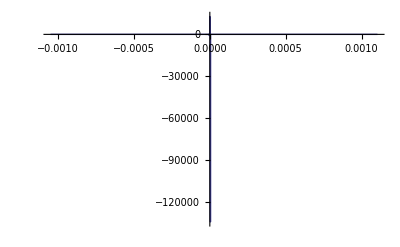

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=1× 10^7
Q2:= 5 × 10^8
Q3:= 4 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=10
x2:=0.0002
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00105;
δ1max:=0.001105;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

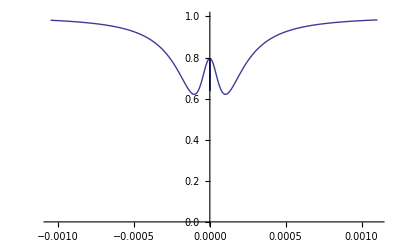

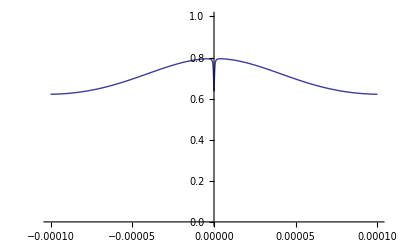

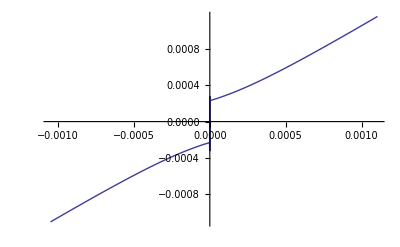

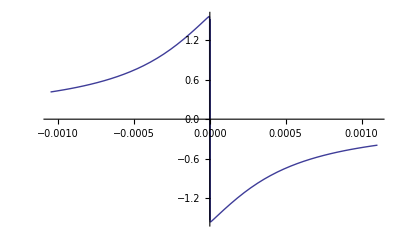

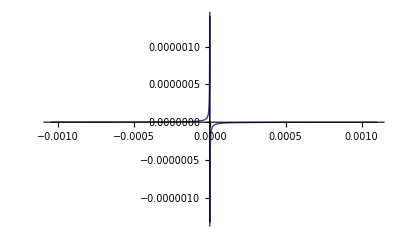

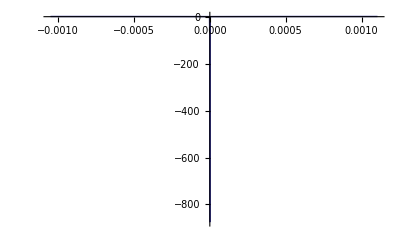

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 100 10^(-6)
R3:= 100 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=8× 10^7
Q2:= 5 × 10^8
Q3:=6 × 10^9
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=10
x2:=0.002
x3:=0.0000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00105;
δ1max:=0.001105;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

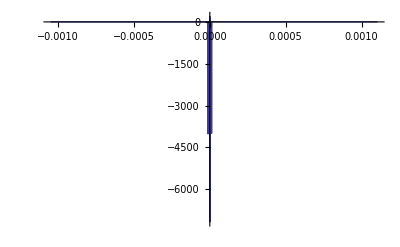

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 200 10^(-6)
R3:= 200 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=5× 10^7
Q2:= 3 × 10^8
Q3:= 9 × 10^8
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=15
x2:=0.00002
x3:=0.000018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00105;
δ1max:=0.001105;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```

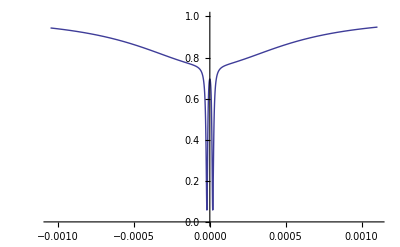

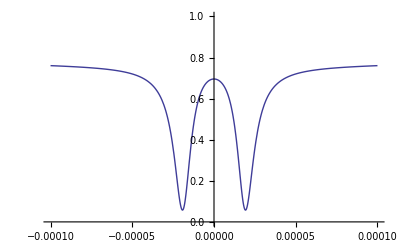

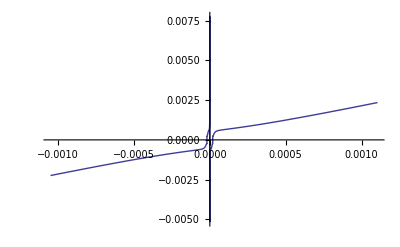

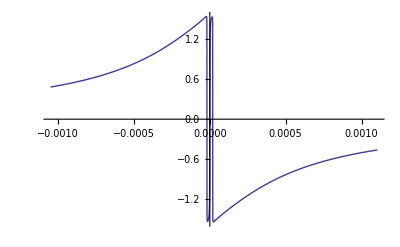

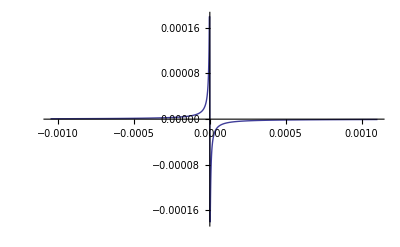

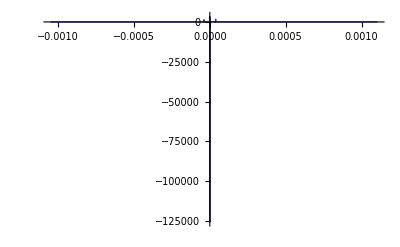

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 200 10^(-6)
R3:= 200 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=5× 10^7
Q2:= 3 × 10^8
Q3:= 9 × 10^8
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=15
x2:=0.0002
x3:=0.00018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00105;
δ1max:=0.001105;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[groupindex,{δ1,δ1min,δ1max}, PlotRange->All]
```

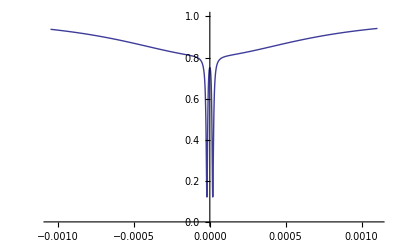

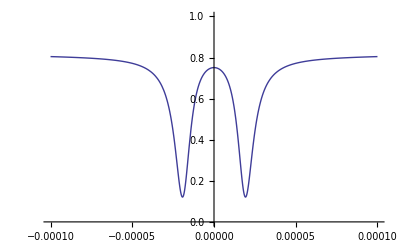

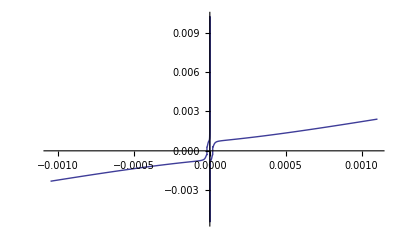

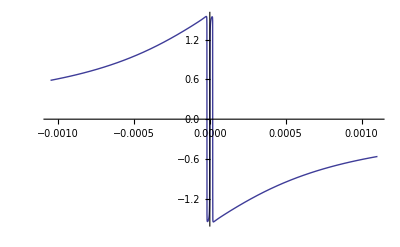

-Graphics-

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 200 10^(-6)
R3:= 200 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=5× 10^7
Q2:= 3 × 10^8
Q3:= 9 × 10^8
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=19
x2:=0.0002
x3:=0.00018
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
(* rat:=((T1 + α1  d1)/(T2 + α2  d2)) *)
s1:=d2/d1  
s2:=d3/d2  
δ2:=s1 δ1
δ3:=s2 δ2
δ1min:=-0.00105;
δ1max:=0.001105;
ref:=Abs[(√(1-T1) - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-√(1-T1) r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))]
r1a:=(√(1-T2) -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-√(1-T2) r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(√(1-T3) -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-√(1-T3) ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[ref^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
 Plot[ref^2,{δ1,-0.0001,0.0001}, PlotRange->{0,1}]
Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
```